```mathematica
n=ConstantArray[1,{23,23}];
m=ConstantArray[1,{11,11}];
```

```mathematica
newMatrix=n;
```

```mathematica
newMatrix[[1;;11,1;;11]]=n[[1;;11,1;;11]]+m;
```

```mathematica
newMatrix//MatrixForm
```

(2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
v={1,1,2,3,4}
```

{1,1,2,3,4}

```mathematica
v-1
```

{0,0,1,2,3}

```mathematica
Total[v]
```

11

```mathematica
Total[v-1]
```

6

```mathematica
m//MatrixForm
```

```mathematica
newMatrix[[23,23]]=1234
```

1234

```mathematica
newMatrix//MatrixForm
```

(2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1234)

```mathematica
A22=({{10.033333333333333, -9.983333333333333, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -9.983333333333333, 10.033333333333333}})
```

{{10.0333,-9.98333,0,0,0,0,0,0,0,0,0},{-9.98333,20.0667,-9.98333,0,0,0,0,0,0,0,0},{0,-9.98333,20.0667,-9.98333,0,0,0,0,0,0,0},{0,0,-9.98333,20.0667,-9.98333,0,0,0,0,0,0},{0,0,0,-9.98333,20.0667,-9.98333,0,0,0,0,0},{0,0,0,0,-9.98333,20.0667,-9.98333,0,0,0,0},{0,0,0,0,0,-9.98333,20.0667,-9.98333,0,0,0},{0,0,0,0,0,0,-9.98333,20.0667,-9.98333,0,0},{0,0,0,0,0,0,0,-9.98333,20.0667,-9.98333,0},{0,0,0,0,0,0,0,0,-9.98333,20.0667,-9.98333},{0,0,0,0,0,0,0,0,0,-9.98333,10.0333}}

```mathematica
B22=({{0.05}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.05}})
```

{0.05,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.05}

```mathematica
LinearSolve[A22,B22]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
0.9999999999999845
```

```mathematica
0.9999999999999843
```

```mathematica
Plot[Piecewise[{{1-x,0<=x<=1}},0],{x,-2,2},PlotRange->All]
```

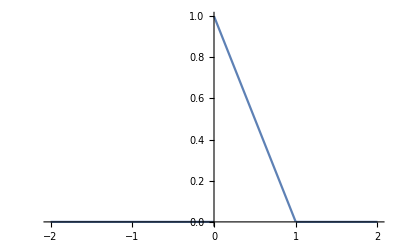
```mathematica
-Graphics-
n=10
```

-Graphics-

10

```mathematica
h=1/n
nodes=ConstantArray[2,n]
```

1/10

{2,2,2,2,2,2,2,2,2,2}

```mathematica
LagrangeP[n1_,p1_]:=Which[n1==2,{InterpolatingPolynomial[{{p1,1},{p1+h,0}},x],InterpolatingPolynomial[{{p1,0},{p1+h,1}},x]}]
```

```mathematica
LagrangeP[2,0]
```

{1-10 x,10 x}

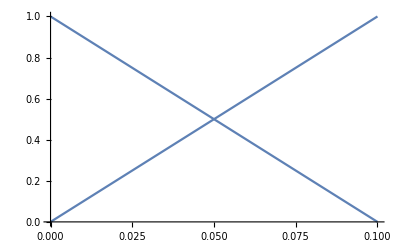

```mathematica
Plot[LagrangeP[2,0],{x,0,h}]
```

```mathematica
LagrangeP[n1_,p1_]:=Which[n1==2,{InterpolatingPolynomial[{{p1,1},{p1+h,0}},x],InterpolatingPolynomial[{{p1,0},{p1+h,1}},x]}]
```

```mathematica
LagrangeP[n1_,p1_]:=Which[n1==2,{Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h,1}},x],p1<=x≤p1+h}},0]},n1==3,{Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h/2,0},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,0},{p1+h,1}},x],p1<=x≤p1+h}},0]}]
```

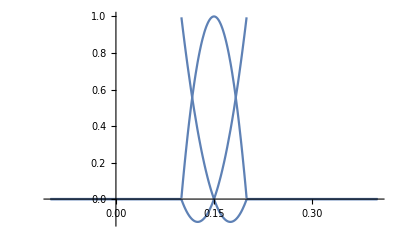

```mathematica
Plot[LagrangeP[3,h],{x,-h,4h},PlotRange->All]
```

```mathematica
ϕ=ConstantArray[0,{n}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
For[i=1,i<=n,i++,
ϕ[[i]]=LagrangeP[nodes[[i]],(i-1)*h]

]
```

```mathematica
LagrangeP[nodes[[4]],(4-1)*h]
```

{Piecewise[{{1-10 (-3/10+x), 3/10≤x≤2/5}, {0, True}}],Piecewise[{{10 (-3/10+x), 3/10≤x≤2/5}, {0, True}}]}

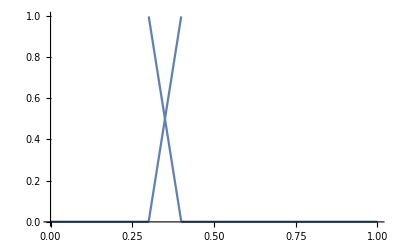

```mathematica
Plot[LagrangeP[nodes[[4]],(4-1)*h],{x,0,1}]
```

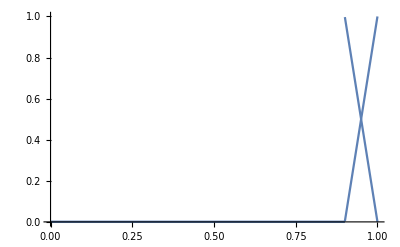

```mathematica
Plot[ϕ[[10]],{x,0,1}]
```

```mathematica
Q[[1]]
```

{Piecewise[{{1-10 x, 0≤x≤1/10}, {0, True}}],Piecewise[{{10 x, 0≤x≤1/10}, {0, True}}]}

```mathematica
Q[[2]]
```

{Null (Piecewise[{{1-10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}]),Null (Piecewise[{{10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}])}

```mathematica
ConstantArray[0,{4}]
```

{0,0,0,0}

```mathematica
A333=({{10.033333333333333, -9.983333333333333, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -9.983333333333333, 20.066666666666666, -9.983333333333333}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -9.983333333333333, 10.033333333333333}})
```

{{10.0333,-9.98333,0,0,0,0,0,0,0,0,0},{-9.98333,20.0667,-9.98333,0,0,0,0,0,0,0,0},{0,-9.98333,20.0667,-9.98333,0,0,0,0,0,0,0},{0,0,-9.98333,20.0667,-9.98333,0,0,0,0,0,0},{0,0,0,-9.98333,20.0667,-9.98333,0,0,0,0,0},{0,0,0,0,-9.98333,20.0667,-9.98333,0,0,0,0},{0,0,0,0,0,-9.98333,20.0667,-9.98333,0,0,0},{0,0,0,0,0,0,-9.98333,20.0667,-9.98333,0,0},{0,0,0,0,0,0,0,-9.98333,20.0667,-9.98333,0},{0,0,0,0,0,0,0,0,-9.98333,20.0667,-9.98333},{0,0,0,0,0,0,0,0,0,-9.98333,10.0333}}

```mathematica
A333[[1,1;;4]]={1,2,3,4}
A333[[1;;4,1]]={1,2,3,4}
A333[[m,m-3;;m]]={2,3,4,1}
A333[[m-3;;m,m]]={2,3,4,1}
```

{1,2,3,4}

{1,2,3,4}

{2,3,4,1}

{2,3,4,1}

```mathematica
A333//MatrixForm
```

(1 | 2 | 3 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 20.0667 | -9.98333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | -9.98333 | 20.0667 | -9.98333 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | -9.98333 | 20.0667 | -9.98333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -9.98333 | 20.0667 | -9.98333 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -9.98333 | 20.0667 | -9.98333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -9.98333 | 20.0667 | -9.98333 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -9.98333 | 20.0667 | -9.98333 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -9.98333 | 20.0667 | -9.98333 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9.98333 | 20.0667 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 3 | 4 | 1)

```mathematica
F333=({{0.05}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.1}, {0.05}})
```

{0.05,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.05}

```mathematica
F333[[1]]=u0
F333[[m]]=u1
F333[[2]]=F333[[2]]-A333[[2,1]]
F333[[3]]=F333[[3]]-A333[[3,1]]
F333[[4]]=F333[[4]]-A333[[4,1]]
F333[[m-1]]=F333[[m-1]]-A333[[m-1,m]]
F333[[m-2]]=F333[[m-2]]-A333[[m-2,m]]
F333[[m-3]]=F333[[m-3]]-A333[[m-3,m]]
```

0

0

-1.9

-2.9

-3.9

-3.9

-2.9

-1.9

```mathematica
m
```

11

```mathematica
F333//MatrixForm
```

(0
-1.9
-2.9
-3.9
0.1
0.1
0.1
-1.9
-2.9
-3.9
0)

```mathematica
A333[[2,1]]
```

-9.98333

```mathematica
F1[[1]]=u0
F1[[m]]=u1
F1[[2]]=F1[[2]]-K1[[2,1]]
F1[[3]]=F1[[3]]-K1[[3,1]]
F1[[4]]=F1[[4]]-K1[[4,1]]
F1[[m-1]]=F1[[m-1]]-K1[[m-1,m]]
F1[[m-2]]=F1[[m-2]]-K1[[m-2,m]]
F1[[m-3]]=F1[[m-3]]-K1[[m-3,m]]


K1[[1,1;;4]]={1,0,0,0}
K1[[1;;4,1]]={1,0,0,0}
K1[[m,m-3;;m]]={0,0,0,1}
K1[[m-3;;m,m]]={0,0,0,1}
```

0

0

8.08333

-2.9

-3.9

6.08333

-2.9

-1.9

{1,0,0,0}

{1,0,0,0}

{0,0,0,1}

{0,0,0,1}

1

2

3

4

5

6

7

8

9

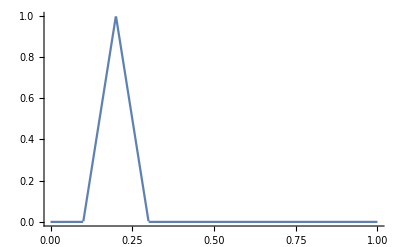

```mathematica
For[i=1,i<n,i++,
Plot[ϕ[[i]][[2]]+ϕ[[i+1]][[1]],{x,0,1},PlotRange->All]
Print[i]
]
```

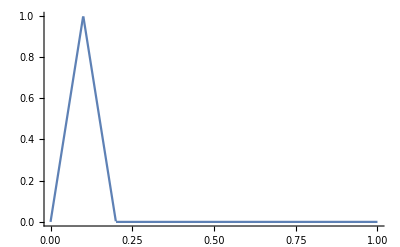

```mathematica
Plot[ϕ[[1]][[2]]+ϕ[[1+1]][[1]],{x,0,1},PlotRange->All]
```

```mathematica
Uh=w[[1]]*ϕ[[1]][[1]]+w[[m]]*ϕ[[n]][[nodes[[n]]]]
```

0.

```mathematica
For[i=1,i<n,i++,
Uh=Uh+w[[i+1]]*(ϕ[[i]][[2]]+ϕ[[i+1]][[1]])
]
```

```mathematica
Plot[Uh,{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
w[[m]]
```

0.

```mathematica
LagrangeP[n1_,p1_]:=Which[n1==2,{Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h,1}},x],p1<=x≤p1+h}},0]},n1==3,{Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h/2,0},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,0},{p1+h,1}},x],p1<=x≤p1+h}},0]}]
```

```mathematica
ϕ
```

{{Piecewise[{{1-10 x, 0≤x≤1/10}, {0, True}}],Piecewise[{{10 x, 0≤x≤1/10}, {0, True}}]},{Piecewise[{{1-10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}],Piecewise[{{10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}]},{Piecewise[{{1-10 (-1/5+x), 1/5≤x≤3/10}, {0, True}}],Piecewise[{{10 (-1/5+x), 1/5≤x≤3/10}, {0, True}}]},{Piecewise[{{1-10 (-3/10+x), 3/10≤x≤2/5}, {0, True}}],Piecewise[{{10 (-3/10+x), 3/10≤x≤2/5}, {0, True}}]},{Piecewise[{{1-10 (-2/5+x), 2/5≤x≤1/2}, {0, True}}],Piecewise[{{10 (-2/5+x), 2/5≤x≤1/2}, {0, True}}]},{Piecewise[{{1-10 (-1/2+x), 1/2≤x≤3/5}, {0, True}}],Piecewise[{{10 (-1/2+x), 1/2≤x≤3/5}, {0, True}}]},{Piecewise[{{1-10 (-3/5+x), 3/5≤x≤7/10}, {0, True}}],Piecewise[{{10 (-3/5+x), 3/5≤x≤7/10}, {0, True}}]},{Piecewise[{{1-10 (-7/10+x), 7/10≤x≤4/5}, {0, True}}],Piecewise[{{10 (-7/10+x), 7/10≤x≤4/5}, {0, True}}]},{Piecewise[{{1-10 (-4/5+x), 4/5≤x≤9/10}, {0, True}}],Piecewise[{{10 (-4/5+x), 4/5≤x≤9/10}, {0, True}}]},{Piecewise[{{1-10 (-9/10+x), 9/10≤x≤1}, {0, True}}],Piecewise[{{10 (-9/10+x), 9/10≤x≤1}, {0, True}}]}}

```mathematica
ϕ1=
```

```mathematica
LagrangeP[n1_,p1_]:=Which[n1==2,{Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h,1}},x],p1<=x≤p1+h}},0]},n1==3,{Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h/2,0},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,0},{p1+h,1}},x],p1<=x≤p1+h}},0]}]
```

```mathematica
(*For[i=1,i<=n,i++,
Ξ=LagrangeP[nodes[[i]],(i-1)*h]

]*)
```

```mathematica
l={}
AppendTo[l,Sin[x]]
```

{}

{Sin[x]}

```mathematica
AppendTo[l,Cos[x]]
```

{Sin[x],Cos[x]}

```mathematica
Ξ={}
```

{}

```mathematica
For[i=1,i<=n,i++,
For[j=1,j≤nodes[[i]],j++,
AppendTo[Ξ,LagrangeP[nodes[[i]],(i-1)*h][[j]]]
]
]
```

```mathematica
AppendTo[Ξ,LagrangeP[nodes[[1]],(1-1)*h][[1]]]
```

{Piecewise[{{1-10 x, 0≤x≤1/10}, {0, True}}]}

```mathematica
Ξ
```

{}

```mathematica
AppendTo[Ξ,LagrangeP[nodes[[2]],(2-1)*h][[1]]]
AppendTo[Ξ,LagrangeP[nodes[[3]],(3-1)*h][[1]]]
```

{Piecewise[{{1-10 x, 0≤x≤1/10}, {0, True}}],Piecewise[{{1-10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}]}

{Piecewise[{{1-10 x, 0≤x≤1/10}, {0, True}}],Piecewise[{{1-10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}],Piecewise[{{1-10 (-1/5+x), 1/5≤x≤3/10}, {0, True}}]}

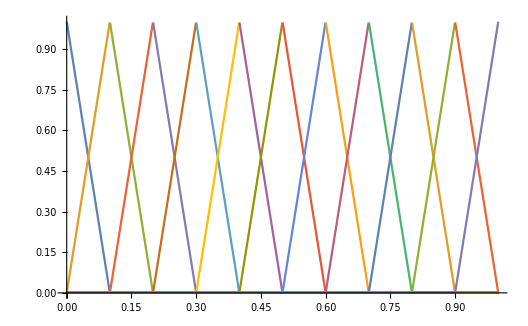

```mathematica
Plot[Ξ,{x,0,1}]
```

```mathematica
Ξ
```

{Piecewise[{{1-10 x, 0≤x≤1/10}, {0, True}}],Piecewise[{{10 x, 0≤x≤1/10}, {0, True}}],Piecewise[{{1-10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}],Piecewise[{{10 (-1/10+x), 1/10≤x≤1/5}, {0, True}}],Piecewise[{{1-10 (-1/5+x), 1/5≤x≤3/10}, {0, True}}],Piecewise[{{10 (-1/5+x), 1/5≤x≤3/10}, {0, True}}],Piecewise[{{1-10 (-3/10+x), 3/10≤x≤2/5}, {0, True}}],Piecewise[{{10 (-3/10+x), 3/10≤x≤2/5}, {0, True}}],Piecewise[{{1-10 (-2/5+x), 2/5≤x≤1/2}, {0, True}}],Piecewise[{{10 (-2/5+x), 2/5≤x≤1/2}, {0, True}}],Piecewise[{{1-10 (-1/2+x), 1/2≤x≤3/5}, {0, True}}],Piecewise[{{10 (-1/2+x), 1/2≤x≤3/5}, {0, True}}],Piecewise[{{1-10 (-3/5+x), 3/5≤x≤7/10}, {0, True}}],Piecewise[{{10 (-3/5+x), 3/5≤x≤7/10}, {0, True}}],Piecewise[{{1-10 (-7/10+x), 7/10≤x≤4/5}, {0, True}}],Piecewise[{{10 (-7/10+x), 7/10≤x≤4/5}, {0, True}}],Piecewise[{{1-10 (-4/5+x), 4/5≤x≤9/10}, {0, True}}],Piecewise[{{10 (-4/5+x), 4/5≤x≤9/10}, {0, True}}],Piecewise[{{1-10 (-9/10+x), 9/10≤x≤1}, {0, True}}],Piecewise[{{10 (-9/10+x), 9/10≤x≤1}, {0, True}}]}

```mathematica
l={}
```

{}

```mathematica
l=ConstantArray[a,{11}]
```

{a,a,a,a,a,a,a,a,a,a,a}

```mathematica
l=Join[l,ConstantArray[b,{2}]]
```

{a,a,a,a,a,a,a,a,a,a,a,b,b}

```mathematica
ConstantArray[a,{11}]
```

{a,a,a,a,a,a,a,a,a,a,a}

```mathematica
Join[{a,b,c},{x,y},{u,v,w}]
```

{a,b,c,x,y,u,v,{0.,0.0413162,0.0730296,0.0954578,0.108826,0.113267,0.108826,0.0954578,0.0730296,0.0413162,0.}}

```mathematica
W1={1}
```

{1}

```mathematica
For[i=2,i<m,i++,
Which[nodes[[i-1]]==2,W1=Join[W1,ConstantArray[i,{2}]],
nodes[[i-1]]==3&&i≠m-1,W1=Join[Join[W1,ConstantArray[i,{1}]],ConstantArray[i+1,{2}]];i=i+1,
nodes[[i-1]]==3&&i==m-1,W1=Join[W1,ConstantArray[i,{1}]]]
]
W1=Join[W1,{m}]
```

{1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10}

```mathematica
W1
```

{1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10}

```mathematica
Which[1==1&&2==3,q=2;q++,1==2,q=20;q+=4,1==1&&2==2&&3==3,q=77]
```

77

```mathematica
q
```

3

```mathematica
n
```

10

```mathematica
(*
w1={w[[1]]
For[i=2,i<n,i++,
Which[nodes[[i-1]]==2,W1=Join[W1,ConstantArray[w[[i]],{2}]],
nodes[[i-1]]==3,W1=Join[Join[W1,ConstantArray[w[[i]],{1}]],ConstantArray[w[[i+1]],{2}]];i=i+1]
]
W1=Join[W1,{m}]


W1={w[[1]]}
For[i=2,i<n,i++,
Which[nodes[[i-1]]==2,W1=Join[W1,ConstantArray[w[[i]],{2}]],
nodes[[i-1]]==3&&i≠m-1,W1=Join[Join[W1,ConstantArray[w[[i]],{1}]],ConstantArray[w[[i+1]],{2}]];i=i+1,
nodes[[i-1]]==3&&i==m-1,W1=Join[W1,ConstantArray[i,{1}]]]
]
W1=Join[W1,{m}]
*)
```